```mathematica
AlphaTest[x_]:=97<=x<=122
ToCode[text_]:=Select[ToCharacterCode@ToLowerCase[text],AlphaTest]-97
FromCode[code_]:=FromCharacterCode[code+65]

testo="0001 XHZDR NNOGB MJWNI XNMNY NYLVW WZECX CIMLI PBCIU YKJLJ UYYRW
0051 JDMDW JJBNZ RHAAI ICYVU FVAND LIGXL VLWCR OYNPV WIKJL HROIJ
0101 FOXMZ WMJYI GRNDL IZLIH YYIMC VEUIX CILYM CIHXX JUUNL CZWTV
0151 MYGVI OXMJL CVUYI NFNNW JUISR RZPFD UYKAI ANLDE UKJLG JHYXU
0201 GUIUB WCXEF NYUBW CXEFN WVWOO XGVMU IRGVP CJECI NYMNJ PKVGR
0251 WVWUG NLVLW JPFDN PVLII JGJAY ZUYMN ADBNM JPVRH AAIIC YVDHN
0301 DIGRV MXCIC LVEPZ MYIMI QROIJ JMXZZ ICVMC QRNOX LDJYY RWDEC
0351 GCKPJ HYXWJ DMDWJ VAFVE ULDYG UYKJL JUYGJ ZMJHX RUZAU NLBDJ
0401 PVJOI MCKAY NBIXX GJPAD WIDBC VVIDV CMJWJ UCMNJ PKVGR WVWCO
0451 XLIJN DRHID FGJFZ LIMAO OCYGN XZPIQ NLIRH PUFDR HONLH NXDOL
0501 VUUXX HQNHU RIINY WXHVY UMCYG NMZAP DUCOM YGUCH YYMXW CNNMJ
0551 MKJLD EUIXU OCLVE YMBID UGVWN JMCBU IMRUN CYNXX VUAZW CJMYG
0601 UOJVI YNFYN MORHJ YIDUU ORLVW HDMYY NFMRM OXLVV YICIG NVMRA
0651 CNMVL YMMIO JFDNA ZBODC CXQYG NXZUO NRIIR YGJWJ ANDPC VWYMR
0701 UKAYQ JFZWN ZJPZE UIXXD OZPBI PWMJW HJBOG UYHNH ORXZP FDDIH
0751 RHDMY GUOIJ JVLYN CUILU PWMDU YIICJ MCMXP DWUXQ YQRYO JPVXA
0801 IRMKN LVWTV MCHNA GRIGN ZJATZ MYGUU BNHZA UURII NHVCU AAUDM
0851 OZBYX XFDGP DRCZG CSBYM JHJLI IBOHJ NZWYD ZOVAU ICUVW HDMCB
0901 DYMAU JBNDW UOJYY RMVPL DOCXR MKNMD JLDLU YNLZW YGOUI PIYXH
0951 YNUQN UQXFP CIGNP VAMDP FDDIH RHDLB ZJPZJ HJEYY DNJRF KACHX
1001 YGDFO RGJPC JAHJM OIJLD EIGDT DXHZM YNCCI JNVJG PCUMN FZBIM
1051 CCZDL JYYZM CNYYM JPVWI YNFKA IBAYN BIOJH ONWMN XZWTZ BYMJH
1101 JJWXD GPUUO NCIZO ZUFJB JVICJ MCONG KXYOJ HONPJ UNZUU KAYKX
1151 NZWTV MYAJN ORFZJ PZJMJ OZJLU ONWCN AGRUI RGDNL VWIBR OICCV
1201 ACIWY BJLZX AIRZZ MYZPF DWNZU FZCND PCVLY QJHJB WJWZJ ANVCC
1251 VEPDU CORMA RXPLC VCCYN FGJPQ NHDAY GNNZX LDLBZ OCGXM JOCXQ
1301 YKNLY DNVXA IRUOC CQRNY NMVVY JPHDN WXRNV VYICI YRWJW NMJMO
1351 XXJAG DEUIX HZUGV CYMRU GRMHX XZUMZ LIGXR QRCDN WJWZD WUQJH
1401 JUOJV IINFG NMZAW DICJM YGUYA JWJUN DWXDE CYDUG RFZCN ZAUOD
1451 LVWII EYMJN MJHIN HZUFZ JWXJX ZVCZE YIMOO NUGYI ONLZZ OVUOI
";

testo="0001 DTDRN FTIFA NPLOI WGLDR ETGOI SBOUI DTCRR LTSLE DPUGA UXIPP \\\\
0051 JTSHI GRAQT GRHHF MGODL LTMSO UWESA KHAUO ABOUI VPFUI UPIOM \\\\
0101 SGEHI FURDN UXAQO UFUHR LPNWO KTGXE FSOOI JTELG ADVHN AAFXR \\\\
0151 GGIGA YGAPA FIEOO JGEFH WHIGI WKAQT GSIYE FSIFA JAAPO JIEGI \\\\
0201 LGOLA FDSRP JPRHC SGLRI EEEUA LDRUO EPNRD AGOGO JAAQD GXNXN \\\\
0251 ETDHS EDTUA LIOFO KPNRN VTTWA ACPUO KPMDI FTIQR ABAFH WEEUA \\\\
0301 EDRYE FCELN XJRRR WTMDT LDDXO ERHHS AHAJG ADEUA KIIPA LDPUI \\\\
0351 EPSHD SROOE ARHHT SAQXA KXMKA XPTWO UWEOP GROLN YTGQO SSOUA \\\\
0401 VDRPI DXMDM WCEVA JEEUO LPNWO UDNFE KHOFH WBIEA KIIDF ACIUQ \\\\
0451 MPNWO ZDPUO ETSVO HXAFC APVLG WCEUO KPEUC MAEDP JDLHO JCAPE \\\\
0501 FIOHS HAEQD GGDHL KTCRL FDSWR GXPSO DXTRA YVRDD AGQXE KIOFH \\\\
0551 WKURL WTDDR NXSRL HJOOU EXLVE JKOYO KIRRQ MTLFH ADVLD WQBRP \\\\
0601 GHSRD AEAUO DTPDG SGELN HPRWE WSOSE JPDLN UWIRS LGOQE UWESO \\\\
0651 UDIRV ASIDD SXMSU LPRVO FDCKE IJAQT GXOSO KHOGA JIUWT GKIGO \\\\
0701 FDVRI KTNWI JTTHF JPISI MSEJN ATRRI UWEQO EXNDR UDNOA MSEPA \\\\
0751 HEAUE URHLO JXCRR VPRTU WARXG YXEUC ZTFXD AKOLE VTVRS LGIDV \\\\";

testo=testo20141103="0001 HYRKF RQBCS CPNFC UMPNA FGUDJ FPTDO DIMYC XMBQB FXEZR LIPZH
0051 VRRMC EMASS IVBSH VHVLC EXVSI KXRZG VRVDO XSYEW RWRBC EHNCS
0101 CPBRD FVTDF VIQDZ IMRMH IEEDR ZUHDZ CMIHS EUHZG ZEHMH IEGSC
0151 RVVRH IMAFS IWVDO GVRMR VVPNF JSREW XYEZR ZJVTA VXEZI ETENA
0201 FRGNF ZSNCS JXEZS LRNLD ZEPNG KMRQO UEYKO CXEZD RVGDS ZPCNB
0251 KIPGS ZZVBC EKVTB XIYDR LIEHJ VTNQQ YIEDB UENMQ FVCHG VRFHP
0301 ZPRZZ CSPBV ZSDTS JXNSF RWSNF DEMHC EIRRS XRVHZ GYASC ZRPTW
0351 ZPYZU FGRRG RIYZR UEEHB TSZHB TMNOS IVVOW XPVZF GSVMC DIQHZ
0401 RKBCC MIYDF ZZRZZ CSASO EEACC JMQHB LSINZ RWPHO EPNBE LEQHG
0451 KIACS IWVDF RPYDB KEERW ZRATC MMTNZ WMRHB EYBUW JIAHZ RGBRH
0501 ZIEZT FVZZH RHNKR VTBRW KSQHH IITQC JWVSC IVRMH ZWPDB UINOD
0551 FKTHO KENCI VQBMH ZGBMH ZKHHZ LRBCS KXBCW JEALO IXVMC CEYSF
0601 FGBMJ FGRKC DFNQR RMYQS JITNB VHNHA FPGHG LSVBC TYMYC CMVMT
0651 ZPNBV VMAUS ISYNT RRANG FQVFZ ZEEDO LRNRS XEGZZ TLANB TLVZZ
0701 GVVLC MIQDF CSCTF TLFHO UMSQC EXRBC DICDF VWRLD ZSQHG LPRLI
0751 IEQHA ZPNMC TLRFI RVQZB FEFDH KIASF ZSADB FRYNR ZWPDF EEGNG
0801 KSNTB KEYBC EXEZG JITMC ZRDTS CPNKI EKNDJ RWGZU ZSTZW RHNFZ
0851 ZEYSF ZQBMH ZHVMC DICHC JGHQC VHVEC IQNOW TSZTB VTRQI EFHNB
0901 GIMYC CEPNG KEFZZ VGBMI ETRMR ZSYDB KSRBC EXVMI FTBHG ZVBLD
0951 VMAOC XKVDW EZNKZ FRPDZ CMVMS IXRDW EMFOW RRNSS JIPNB USYNG
1001 JEGTF RHRCI VQBMH ZIVKZ RZBQC UIYKO TUHDW CPRLP FIFSF VQBSO
1051 XPVZH FHNKZ VJBBW UIGNF IIASW HYNRW KYGSC XLVZW RIPHC KXBKC
1101 EMVKF VWGNQ RQCHS MMTMS JTNQG VHVSS IVRCW MMYKS UMPZG RPVHB
1151 HYNKQ YICZF KIONG TLVBV VWVOF FPHMU RRBRI GIEKO DSASO XRNKS
1201 TGBKO GVVMQ ZTNKS UMDTS CPRSS IVRDQ YIQMC DINKH VVEHH FVVNU
1251 ZEPDD FGBCW JGBRH FHNKD FRGDO CPNQW MEQDZ CETNO EDVUW VRRHB
1301 GEESS RXENJ RVFHB VPYZU FWGDG JSDTO EHBPI VWGNW EKENG JEHMU
1351 IEAAC IKBZZ XMBQB FHBFU ZIPGS JMABO DQVMO RHVUS EXNQQ ZXGZW
1401 KIZOW ZRPTW RGPZR UIENW WEGSW TLROF VRQHO DSNQO TGBMH RVRPI
1451 VPONF XSTHQ FRFHR VVNAW CIRQO RRPGS LRPZG KIYKC VEIDJ RTRQQ
1501 ZPBMC IIQZZ CSTFW RVRTB TSZZB UEASS VMYUO EXNFU ZSQHD FWFDR
1551 VVRTB RWGZP ZPRFI RVAHU ZSADR ZWBKR RXVRD RKANZ ZGUDW EWRFB
1601 RZNMZ RQBCS JXVZO CPREO EGVTZ CIRZZ CIQNB EIQDZ GERRS RGPZF
1651 VDMZJ RRQHH VQCNW EXRLD FPRRD RPYDO HYNKQ YIZZF ZXBZE LEYBV
1701 VTNCF VIFTZ WMAHF UIYKS JXNSS ESALO EGNUO EQNHR ZWCZB UIERW
1751 EIYKS MMTMS GIECW IEQZF CYIDS RPYDU XIEHF VEPNB KEQHB ZPREO
1801 KMPGS UIYKO MIACS DQVZR RPYTB REYKO CXEZR ZUHDZ CIGDF IIQZZ
1851 CEYSI IINKZ RVVUO UEHMD FKTHC RPYZZ KVBBC IVRUO ESRBC IVBMC
1901 KYGSO MMNRH IEQDS JXEZR VXGDD ZSZDB IMCHR VSCHO EIBFB ZXNMH
1951 FESEC EHNSS JICNZ KIGQO UYRLI IMQNB UINKN RRQNZ FWTTO IHBMC";

testo="AITOPQPAGLYSKWVAYTXMJOCOHBGQHSAXWCPOIWJFBFQMFDBZPIUACSATADRZRIHOPVTTDINJTIVIESIZGGHOHBGPBWRWEIAQXWLUIIDKZIBFXVGVRZAQVIFDTZSTBRDTGRPVTTUOEAXXJEZSVQSPHFEMFSNBSWHRVORPAOASUINEYZXUSSRZTUAECOGWDERGHMJDVSCAWMRQWMXRHHIQANSOBQSAYHGIVIGCGKZIECSWHAEZPZWEYOVZAMNFKMVRNWXVKIRATQGNBBHWUHVHJAWNCSGKZEZCSWNEAIIWKEDIPOAUZOUQGRRBIQFOZWHMEBEWKMJAZSCBWQHOCLAOGCSWLUQSXASPRFRPAFHWRWFTRIVWDIACTYMEFHXTSRPWKMKCBJDZMGTWTZAOEHXLARBDTZUHVGDVLAYJXKANBPGMNECSGBMGVCSMFTECSIDAZISIDADIPTHEEATPSLGWIWDDRZPNSMRSRPWCBBKQWNROCKGRPVPTLRHWHQUHVISIEAISPUGSGFPBGPRFAWKUBTDZSMRDXCDUASVQSQHOCLAOSSRQDMNZHWFNBQWMVEYTJBMRBAXAIUNFRQGLISAIEEDITALICOGMNANATUSEFHGWWDBBCWUAPQXIFDBWATMPBSACHIPWCQSLZCCBWPRFRPWICWHIFVRRTZDUPQPVGNCCCVGCBBRIYNRAPOJEFHJLAOFSTKGNGSVCSLNBSQUOAGXAEOARXMUOAZPVXRNBRPASNJTIEEFGXLANNBOQVAYOUZGNGSXVHIPQXWDCBFHWEICOGDWRPCIIDIPVTTHAQFTMAFVUAQWRNBAIEOEHXQFSVSBMWIBJXLACVOHKMNPOSMJTEO"
```

AITOPQPAGLYSKWVAYTXMJOCOHBGQHSAXWCPOIWJFBFQMFDBZPIUACSATADRZRIHOPVTTDINJTIVIESIZGGHOHBGPBWRWEIAQXWLUIIDKZIBFXVGVRZAQVIFDTZSTBRDTGRPVTTUOEAXXJEZSVQSPHFEMFSNBSWHRVORPAOASUINEYZXUSSRZTUAECOGWDERGHMJDVSCAWMRQWMXRHHIQANSOBQSAYHGIVIGCGKZIECSWHAEZPZWEYOVZAMNFKMVRNWXVKIRATQGNBBHWUHVHJAWNCSGKZEZCSWNEAIIWKEDIPOAUZOUQGRRBIQFOZWHMEBEWKMJAZSCBWQHOCLAOGCSWLUQSXASPRFRPAFHWRWFTRIVWDIACTYMEFHXTSRPWKMKCBJDZMGTWTZAOEHXLARBDTZUHVGDVLAYJXKANBPGMNECSGBMGVCSMFTECSIDAZISIDADIPTHEEATPSLGWIWDDRZPNSMRSRPWCBBKQWNROCKGRPVPTLRHWHQUHVISIEAISPUGSGFPBGPRFAWKUBTDZSMRDXCDUASVQSQHOCLAOSSRQDMNZHWFNBQWMVEYTJBMRBAXAIUNFRQGLISAIEEDITALICOGMNANATUSEFHGWWDBBCWUAPQXIFDBWATMPBSACHIPWCQSLZCCBWPRFRPWICWHIFVRRTZDUPQPVGNCCCVGCBBRIYNRAPOJEFHJLAOFSTKGNGSVCSLNBSQUOAGXAEOARXMUOAZPVXRNBRPASNJTIEEFGXLANNBOQVAYOUZGNGSXVHIPQXWDCBFHWEICOGDWRPCIIDIPVTTHAQFTMAFVUAQWRNBAIEOEHXQFSVSBMWIBJXLACVOHKMNPOSMJTEO

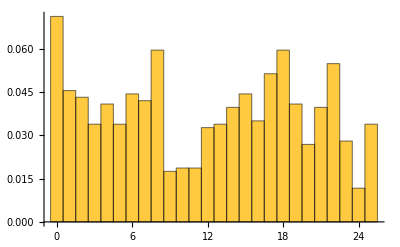

```mathematica
ciphertext=ToCode[testo];
Histogram[ciphertext,26,"Probability"]
```

```mathematica
Map[Count[ciphertext,#]&,Range[1,25]]/Length[ciphertext]
Distribution[text_]:=Map[Count[text,#]&,Range[0,25]]/Length[text]
CoincidenceIndex[text_]:=Apply[Plus,Distribution[text]^2]

Distinguisher[text_,t_]:=N@CoincidenceIndex[Take[text,t]]-{0.038,0.068,0.072}
```

{1/22,37/858,29/858,35/858,29/858,19/429,6/143,17/286,5/286,8/429,8/429,14/429,29/858,17/429,19/429,5/143,2/39,17/286,35/858,23/858,17/429,47/858,4/143,5/429,29/858}

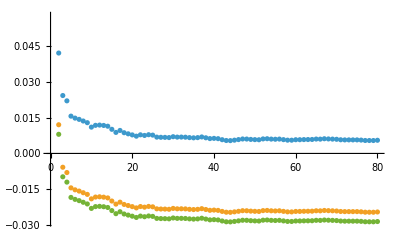

```mathematica
distinguishers=Transpose[Table[Distinguisher[ciphertext,t],{t,10,800,10}]];
ListPlot[distinguishers]
```

```mathematica
N@CoincidenceIndex[ciphertext]
```

0.0433246

```mathematica
TruncatedCoincidenceIndex[text_,t_,n_]:=Apply[Plus,Take[Sort@N@Distribution[Take[text,t]],-n]^2]
ITA=ToCode@Import["http://www.corriere.it"];
IcITA=N@CoincidenceIndex[ITA]
```

0.075007

```mathematica
TruncatedCoincidenceIndex[ciphertext,All,7]
```

0.0217791

```mathematica
IcITA5=N@TruncatedCoincidenceIndex[ITA,Length[ITA],5]
```

0.0540359

```mathematica
IcITA7=N@TruncatedCoincidenceIndex[ITA,Length[ITA],7]
IcITA10=N@TruncatedCoincidenceIndex[ITA,Length[ITA],10]
ENG=ToCode@Import["http://www.nytimes.com"];
IcENG=N@CoincidenceIndex[ENG]
IcENG5=N@TruncatedCoincidenceIndex[ENG,Length[ENG],5]
IcENG7=N@TruncatedCoincidenceIndex[ENG,Length[ENG],7]
IcENG10=N@TruncatedCoincidenceIndex[ENG,Length[ENG],10]
IcRND=N@1/26
IcRND5=N@5/26^2
IcRND7=N@7/26^2
IcRND10=N@10/26^2
{IcRND5,IcENG5,IcITA5}
```

0.0624734

0.0699179

0.0643865

0.0399842

0.049732

0.0574461

0.0384615

0.00739645

0.010355

0.0147929

{0.00739645,0.0399842,0.0540359}

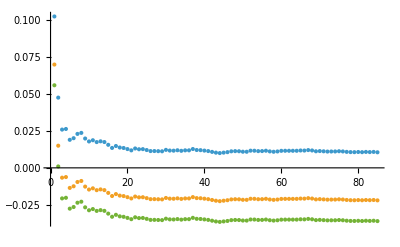

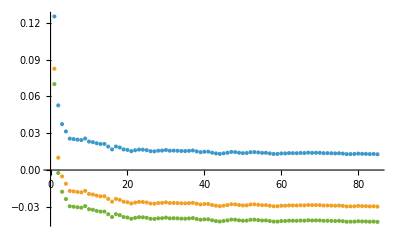

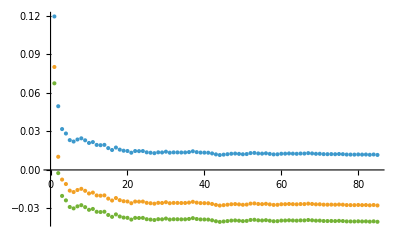

```mathematica
ListPlot@Transpose[Table[TruncatedCoincidenceIndex[ciphertext,t,5]-{IcRND5,IcENG5,IcITA5},{t,10,Length[ciphertext],10}]]
ListPlot@Transpose[Table[TruncatedCoincidenceIndex[ciphertext,t,10]-{IcRND10,IcENG10,IcITA10},{t,10,Length[ciphertext],10}]]
ListPlot@Transpose[Table[TruncatedCoincidenceIndex[ciphertext,t,7]-{IcRND7,IcENG7,IcITA7},{t,10,Length[ciphertext],10}]]
```

```mathematica
(* KASISKI TEST *)

(*trovo blocchi ripetuti nel testo *)


Distances[parted_,rep_]:=Flatten@Position[parted,rep]

KasiskiTest[text_,len_]:=Module[{nparted,nreps,ndd},
parted=Partition[text,len,1];
reps=SortBy[Select[Tally[parted],#[[2]]==2&],Last];
dd=Sort@Map[Distances[parted,#[[1]]]&,reps];
     distanze=Flatten@Map[Drop[#,1]-Drop[#,-1]&,dd];
Apply[GCD,distanze]
]

(* ipotesi di lunghezza chiave *)
mguess=KasiskiTest[ciphertext,6]

(* controllo i fattori per capire se il guess è verosimile *)
Map[FactorInteger,distanze]//TableForm
```

216

2
3 | 3
3
2
3 | 3
3

```mathematica
reps
Map[FromCode,reps]
```

{{{7,14,2,11,0,14},2},{{16,7,14,2,11,0},2}}

{{HOCLAO,C},{QHOCLA,C}}

```mathematica
FactorInteger[Subtract@@Flatten@Position[parted,{17,18,11,6}]]
FromCode@{17,18,11,6}
```

Subtract::argrx: Subtract called with 0 arguments; 2 arguments are expected.

FactorInteger::exact: Argument Subtract[] in FactorInteger[Subtract[]] is not an exact number.

FactorInteger[Subtract[]]

RSLG

```mathematica
FactorInteger[646-76]
```

{{2,1},{3,1},{5,1},{19,1}}

```mathematica
dd
```

{{27,87},{75,380},{76,646},{121,421},{222,297},{279,479},{340,440},{433,548},{639,794}}

```mathematica
(* divido il ciphertext in blocchi di testo nelle posizioni modulo mguess *)
mguess=6
blocks=Transpose[Partition[ciphertext,mguess]];

(* come verifica di mguess, calcolo l'índice di coincidenza per ogni blocco*)
N@Map[TruncatedCoincidenceIndex[#,100,7]&,blocks]
```

6

{0.0538,0.0793,0.0573,0.0584,0.0614,0.0699}

```mathematica
deng=N@Distribution[ENG]
ArgMaxFreq[dita_]:=Position[dita,Max[dita]]-1

(* calcolo la n-esima più frequente *)
ArgMaxFreq[dita_,n_]:=Position[dita,Sort[dita][[-n]]]-1

mfITA=ArgMaxFreq[Distribution[ITA]][[1,1]]
mfENG=ArgMaxFreq[Distribution[ENG]]


(* i problemi a lezione nascono dalla differenza di distribuzione della prima pagina del corriere e quella del testo*)
```

{0.086793,0.0130956,0.0338534,0.0388688,0.112705,0.0206186,0.0157425,0.0397047,0.0809418,0.00236835,0.00947339,0.0401226,0.0316244,0.0682641,0.0713291,0.0280022,0.000278629,0.071747,0.0672889,0.0897186,0.0293954,0.0100306,0.0190861,0.00181109,0.0149067,0.00222903}

8

{{4}}

```mathematica
ClearAll[Plot]
```

ClearAll::wrsym: Symbol Plot is Protected.

```mathematica
PlotDistribution[distribution_,color_]:=ListLinePlot[Transpose[{Range[0,25],distribution}],
PlotTheme->"Business",
Filling->Automatic,
InterpolationOrder->2,
PlotStyle->color
];

PlotText[text_,color_]:=PlotDistribution[Distribution[text],color];
```

```mathematica
Dec[key_,y_]:=Mod[y-key,26]
```

```mathematica
dita
```

dita

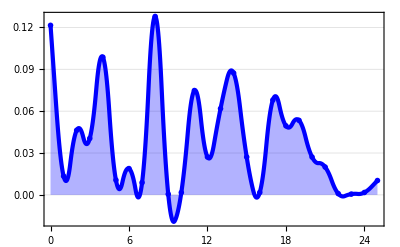

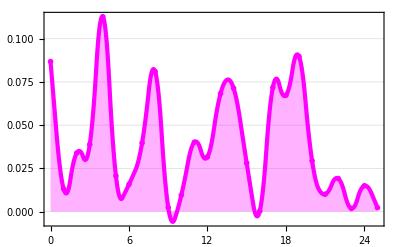

```mathematica
itaplot=PlotText[ITA,Blue]
engplot=PlotText[ENG,Magenta]
```

```mathematica
PlotBlock[blk_][key_]:=PlotText[
Map[Dec[key,#]&,blocks[[blk]]],Orange]

Manipulate[Show[itaplot,PlotBlock[b][k]],{b,1,mguess,1},{k,0,25,1}]
```

```mathematica
FromCode[keyguess={15,8,18,0,13,14}]
```

PISANO

```mathematica
keyguess=Mod[Flatten@Map[ArgMaxFreq[Distribution[#],1]&,blocks]-mfITA,26]
Mod[Flatten@Map[ArgMaxFreq[Distribution[#],2]&,blocks]-mfITA,26]
Mod[Flatten@Map[ArgMaxFreq[Distribution[#],3]&,blocks]-mfITA,26]
```

{15,14,18,22,0,19,10}

{11,4,8,24,22,0,9,6}

{7,4,8,10,14,6,7,14}

```mathematica
MutualIncidence[text1_,text2_]:=N@Apply[Plus,Distribution[text1]*Distribution[text2]]
```

{0.11393,0.0104929,0.0445833,0.0413422,0.108753,0.0110992,0.0198433,0.00881407,0.12405,0.0003964,0.00114256,0.0698829,0.0270251,0.067388,0.0907755,0.026279,0.00195868,0.0701394,0.0465653,0.060346,0.0257893,0.0170918,0.00111925,0.000536306,0.00142238,0.00923378}

```mathematica
decifrato=Mod[blocks-keyguess,26];
Map[MutualIncidence[ITA,#]&,decifrato]
plaintext=FromCode[ptx=Flatten@Transpose@decifrato]
```

Thread::tdlen: Objects of unequal length in {{0,15,10,23,7,0,8,16,15,0,17,19,19,8,7,17,23,3,23,0,19,3,19,23,21,4,18,17,20,23,19,6,7,2,22,8,1,6,6,18,15,21,10,23,19,7,9,6,18,8,«93»},«4»,{16,18,19,14,18,14,5,25,18,25,21,9,18,14,22,16,8,5,25,3,17,21,0,18,5,1,14,18,25,25,14,6,18,16,7,14,7,2,2,25,14,5,22,0,1,7,18,2,8,8,«93»}}+{-15,-14,-18,-22,0,-19,-10} cannot be combined.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Indeterminate

FromCharacterCode::intnm: Non-negative machine-sized integer expected at position 1 in FromCharacterCode[65+Mod[{«1»}+{-15,-14,-18,-22,0,-19,-10},26]^T].

FromCharacterCode[65+Transpose[Mod[{{0,15,10,23,7,0,8,16,15,0,17,19,19,8,7,17,23,3,23,0,19,3,19,23,21,4,18,17,20,23,19,6,7,2,22,8,1,6,6,18,15,21,10,23,19,7,9,6,18,8,15,20,8,7,10,2,2,18,23,17,17,21,19,23,10,3,19,23,19,3,23,6,6,18,18,18,15,19,8,15,17,10,2,15,7,18,15,15,0,3,23,21,2,17,7,22,9,23,17,0,19,6,19,6,2,23,0,0,2,2,17,7,19,15,2,17,15,9,19,21,18,23,23,15,17,19,23,14,20,23,23,7,6,8,19,19,0,0,23,1,23,7,18},{8,0,22,12,1,23,22,12,8,19,8,19,8,25,1,22,22,10,21,16,25,19,19,23,16,12,22,15,8,20,20,22,12,0,12,16,16,8,10,22,25,25,12,21,16,22,0,10,22,22,14,16,16,12,12,1,11,22,0,15,22,22,24,19,12,25,25,11,25,21,10,12,1,12,8,8,19,15,22,13,15,16,10,19,16,8,20,1,22,25,2,16,11,16,22,12,1,0,16,8,0,12,20,22,22,8,19,2,16,1,15,8,25,21,21,8,14,11,10,2,16,0,12,21,15,8,11,16,25,21,22,22,3,8,19,12,16,8,16,12,11,10,12},{19,6,21,9,6,22,9,5,20,0,7,3,21,6,6,4,11,25,6,21,18,6,20,9,18,5,7,0,13,18,0,3,9,22,23,0,18,21,25,7,22,0,21,10,6,20,22,25,13,10,0,6,5,4,9,22,0,11,18,0,5,3,12,18,10,12,0,0,20,11,0,13,12,5,3,3,7,18,3,18,22,22,6,11,20,4,6,6,10,18,3,18,0,3,5,21,12,8,6,4,11,13,18,22,20,5,12,7,18,22,22,5,3,6,6,24,9,0,6,18,20,4,20,23,0,4,0,21,6,7,3,4,22,3,7,0,22,4,5,22,0,12,9},{14,11,0,14,16,2,5,3,0,3,14,8,8,6,15,8,20,8,21,8,19,17,14,4,15,18,17,14,4,18,4,4,3,12,17,13,0,8,8,0,4,12,17,8,13,7,13,4,4,4,20,17,14,1,0,16,14,20,15,5,19,8,4,17,2,6,14,17,7,0,13,4,6,19,0,0,4,11,3,12,2,13,17,17,7,0,18,15,20,12,20,16,14,12,13,4,17,20,11,4,8,0,4,3,0,3,15,8,11,15,8,21,20,13,2,13,4,14,13,11,14,14,14,17,18,4,13,0,13,8,2,8,17,8,0,5,17,14,18,8,2,13,19},{15,24,24,2,7,15,1,1,2,17,15,13,4,7,1,0,8,1,17,5,1,15,4,25,7,13,21,0,24,17,2,17,21,17,7,18,24,6,4,4,24,13,13,17,1,21,2,25,0,3,25,17,25,4,25,7,6,16,17,7,17,0,5,15,1,19,4,1,21,24,1,2,21,4,25,3,4,6,17,17,1,17,15,7,21,8,6,17,1,17,0,7,18,13,1,24,1,13,8,3,2,13,5,1,15,1,1,15,25,17,2,17,15,2,1,17,5,5,6,13,0,0,0,13,13,5,13,24,6,15,1,2,15,15,16,21,13,4,21,1,21,15,4},{16,18,19,14,18,14,5,25,18,25,21,9,18,14,22,16,8,5,25,3,17,21,0,18,5,1,14,18,25,25,14,6,18,16,7,14,7,2,2,25,14,5,22,0,1,7,18,2,8,8,14,1,22,22,18,14,2,18,5,22,8,2,7,22,9,22,7,3,6,9,15,18,2,2,8,8,0,22,25,18,1,14,21,22,8,18,5,5,19,3,18,14,18,25,16,19,0,5,18,8,14,0,7,1,16,22,18,22,2,5,22,17,16,2,1,0,7,18,18,1,6,17,25,1,9,6,1,14,18,16,5,14,2,21,5,20,1,7,18,9,14,14,14}}+{-15,-14,-18,-22,0,-19,-10},26]]]

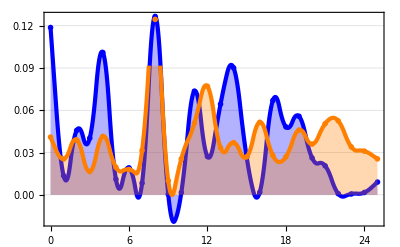

```mathematica
(* mostriamo che la distribuzione di riferimento per l'italiano (homepage del Corriere) non era coerente con le frequenze del plaintext : inversione tra le due lettere più frequenti la E nel plaintext e la I nel corriere (per questo motivo 
nella crittoanalisi in classe abbiamo dovuto scegliere sempre di decifrare con la seconda lettera più frequente )*)
Show[itaplot,PlotText[ptx,Orange]]
```

```mathematica
N@CoincidenceIndex[ITA]
N@CoincidenceIndex[ptx]
MutualIncidence[ITA,ptx]
```

0.0750274

0.051195

0.0487016

```mathematica
plaintext
```

QYMTLAQWLYLPIOIDMKWGOGPMPOPOMUMIHHIGMWZHOXZIXUIKINERMVINMVBYRVWBNEHQUINXQBOTXMIMERQMUGSTNCAWMKINHILYLPWAJOVOMLEILMFRMMVNREZMXIUCMFLMDQYNUCIMIECVNREBBIAVQANRMVOYRWQMUPVMVXEVKWLSSMNCGYZIXIJQCGEXZIONTZWGORBWLISILYSXZIYURIUJIEKWMTMMZUDETTULXZIJAVBMYIPXWHTIKPYIZQKINKQCHGITMXUIZQPETIZWHIZMHDEIVWOVXQMERAQVIPMIFLSKKBISYCYSXIBLAWNWLMEHQINIMAYGRQQFPYVBIIRKCCIPTIAOGMAMAITIXDEZQHCSUQHCMIXYRVQXCGPQILPSQVIMILQFAKWLIVITMLIZMIFLSVBUNEVLISMLQHUSDWFAWKQUNPIKKUELQMTIVLYRWQMLAPTMHTEZACIRVCIVMOWFFMMQHNYWDCSIVQFAGWANIIZIZOVUINAHITXETWACTSLQNRIOZISWQBIRVMVNIWKMHDIIXJOKOQUTEILOEQWVNIGWVNIKCQFURWLYTXWLCSEVUURXQVILETBLOGWVPOGMTIMFIZXAMTZYSIOWHEHIQGOPBQMUSQKICYHHILMQVZIPIKBEMVDYRSTWZARVWMOQQOFIEZMUURIAYGEBIFCLVWHCLQIFPVQUIVILMLLSXCLCLAQUDMNZINXMKIMIXMLEWMUJISLQMUPMUORELQGIPIVICLMOOAVLIHOEAMNTIVBLISVMHORTWXIWKMLNEBWMTSICHTETKINXZIMSIOVIIRYCYLPITONKIMPAWBIAISOICAHIOFIETBLIQWVNIHQVIMIXQISGCZIEHQNIRQIXCCSUCHETMZONFCWHPIHHILEKWMTEAIFEGWVONTMVXISTMHTSMKINXQVOOTWQMIVWUJEMVXIGKQMCNZITFORKMFLMQVYRXMMCNMAXCARIBYSIKWHDSTWMSEBCLAHMLOEQWVNIIQTFAZWZIDITTUCUCMCLPMUVOIABLEQWBUGPQINOHITFEJWKCDIBWLRIVBCQYIACTYBBIGLQICAIKQITXWTINMQTLEWBWWAQXQYVMOVYSTIZMEHQBYRVMLCVMTTYDMKIMAPQQHQYITWHIXILTIJWMCLQKBEWQXLOPCVAARWAOPIZTUMSVBUGRITYCGWTUPVQVWITITYDMYCYLPMBYRVMMWHILVIMIITNEVZQNOVQWAIEKMJOGWLCSGWANOHITJORBMULPIZCVELMFLEOWUNDQDCERMQHPEZBYAXZWPAVAQHEPTIAOWBMMSSYCUNHWYOEWBWCNKZWMSECVAREVJIRKWIFGMWZHOHWOAIIKPYSMVKUMQQVUAHQDYNXIZWIXBICTIUXCIRKCCAGKIXDIZWCFEBBCCLMXLERLQUMSIZUCGWVNAVMYOEPJWLGSOQWORAQXEVIJCLIMZUARKPYURKIMTITTIEEDMPATMZWIPWVIRILIFLSOOCAVMCHCSUIHDEVBYEMTDUNXIOAISLQJOWAMXEVMCHAWBIVIPMOOAVVQAISVMXIWWTXAXQAJAKVWFIGPMCNWMOHAZIVFAQWLYSXQIULPMNUNGQCFLIMIFLILWHNILMFPEMAYAGKILEDHIPARLQNEQXWCNXMUJOPMAJAPTMUQYITWHIUILIXWIKUETKBETILLEIACFFMVQLDITTYSXIBYNSVUUNGIDUNQIQXIWXIHDIZACNITTYVMOVYPIZLCRELILLYDMYAPTMAGIZQLEEKWHTELQHIPMNUTMKPYDITTUVIVLYMQQIXAPTCHAETTULXZIXIUCMFLIBMLRILIFLETBORIITFAVQDUDECVJOKOQIAPTIFTVWKIRVMDUNSMKIRVWVITYBBUVMIANRELMYSXZIXEXBMJISUMHRMXQXESXQUNIWOHIXIVNOENNINHIBYSIXWFTIBZUDYMUORMLWHDIITTARLWFOWOCURHWVI

```mathematica
rnd=RandomInteger[25,100]
```

{19,9,12,6,24,18,20,5,25,7,13,4,4,10,17,12,23,25,0,25,15,0,4,13,7,4,17,1,25,17,9,6,10,22,2,24,12,24,20,19,4,15,9,16,16,19,24,18,8,18,15,21,1,24,8,23,6,4,3,14,11,15,23,7,5,20,2,14,25,23,7,1,11,3,22,23,6,20,18,0,22,4,20,0,16,13,6,7,24,11,14,20,17,18,6,3,11,8,5,15}

```mathematica
(* alcune considerazioni per rendere più efficiente la ricerca soprattutto quando si fa con carta e penna *)

(*Partition[blocks[[1]],5]//TableForm*)

(* stabilisco le lettere più frequenti nei primi 30 caratteri del testo*)
blk =blocks[[2]]

t0=30
troncato0=Take[blk,t0]
st0=SortBy[Tally[troncato0],Last]
ct0=Map[First,Take[st0,-7]]
Print["7 lettere piu' frequenti nei primi ",t0," caratteri di testo : ",FromCode[ct0]]

(* conto il numero di occorrenze di quelle lettere nel testo più lungo (almeno 100 caratteri)*)

t=100;
troncato=Take[blk,t];
SortBy[Tally[troncato],Last];

(* con questa statistica confronto l'indice di coincidenza troncato alle lettere più frequenti *)
conta0=Map[Count[troncato,#]&,ct0];

Print["occorrenze delle prime 7 lettere considerati i primi ",t0," caratteri, contate nei primi ",t," caratteri\n",conta0]

Print["indice di coincidenza troncato ai 7 piu frequenti : ",
N@Apply[Plus,(conta0/t)^2]," (cf. con IcITA7 = ",
IcITA7," e IcRND7 = ",
IcRND7,")\n"]
```

{8,0,22,12,1,23,22,12,8,19,8,19,8,25,1,22,22,10,21,16,25,19,19,23,16,12,22,15,8,20,20,22,12,0,12,16,16,8,10,22,25,25,12,21,16,22,0,10,22,22,14,16,16,12,12,1,11,22,0,15,22,22,24,19,12,25,25,11,25,21,10,12,1,12,8,8,19,15,22,13,15,16,10,19,16,8,20,1,22,25,2,16,11,16,22,12,1,0,16,8,0,12,20,22,22,8,19,2,16,1,15,8,25,21,21,8,14,11,10,2,16,0,12,21,15,8,11,16,25,21,22,22,3,8,19,12,16,8,16,12,11,10,12}

30

{8,0,22,12,1,23,22,12,8,19,8,19,8,25,1,22,22,10,21,16,25,19,19,23,16,12,22,15,8,20}

{{0,1},{10,1},{15,1},{20,1},{21,1},{1,2},{16,2},{23,2},{25,2},{12,3},{19,4},{8,5},{22,5}}

{16,23,25,12,19,8,22}

7 lettere piu' frequenti nei primi 30 caratteri di testo : QXZMTIW

occorrenze delle prime 7 lettere considerati i primi 30 caratteri, contate nei primi 100 caratteri
{12,2,8,12,7,10,16}

indice di coincidenza troncato ai 7 piu frequenti : 0.0761 (cf. con IcITA7 = 0.0624734 e IcRND7 = 0.010355)

```mathematica
(* suggerimenti per il kasiski test a mano : trovare trigrammi ripetuti nei primi 150 caratteri del testo *)

trigrammimultipli=Select[Tally@(parted=Partition[Take[ciphertext,150],3,1]),Last[#]>1&]
Map[FromCode[First[#]]&,trigrammimultipli]

(* e poi cercare solo questi nel testo intero *)

Map[Position[Partition[ciphertext,3,1],#[[1]]]&,trigrammimultipli]//TableForm
```

{{{14,7,1},2},{{7,1,6},2},{{15,21,19},2},{{21,19,19},2}}

{OHB,HBG,PVT,VTT}

24 | 84 | 
25 | 85 | 
65 | 131 | 803
66 | 132 | 804

```mathematica
Map[FromCode[First[#]]&,Select[Tally@Partition[Take[ciphertext,All],5,1],Last[#]>1&]]
```

{QHOCL,HOCLA,OCLAO,PRFRP}

```mathematica
zz={7,17,16,9,9,5,5}
Apply[Plus,N[(zz/117)]^2]
```

{7,17,16,9,9,5,5}

0.0588794

```mathematica
(* cosa succede all'indice di coincidenza dei bloccki se sbagliamo la lunghezza della chiave *)

Table[blocks5=Transpose[Partition[ciphertext,i]];
N[Map[CoincidenceIndex,blocks5]],{i,3,10}]//TableForm
```

0.0563842 | 0.0533767 | 0.0590249 |  |  |  |  |  |  | 
0.0494366 | 0.0532361 | 0.0530614 | 0.0511398 |  |  |  |  |  | 
0.0498273 | 0.046681 | 0.0535207 | 0.0444923 | 0.0492117 |  |  |  |  | 
0.0767275 | 0.0840628 | 0.0718373 | 0.0723263 | 0.0765319 | 0.0770209 |  |  |  | 
0.047971 | 0.0482397 | 0.0552271 | 0.0467616 | 0.0499866 | 0.0483741 | 0.0483741 |  |  | 
0.0516202 | 0.0589571 | 0.0552887 | 0.0530177 | 0.0537165 | 0.0549393 | 0.0608787 | 0.0563368 |  | 
0.0583934 | 0.065928 | 0.0650416 | 0.0643767 | 0.0568421 | 0.0639335 | 0.0621607 | 0.0583934 | 0.0719114 | 
0.0604844 | 0.0555017 | 0.0543945 | 0.0560554 | 0.0621453 | 0.0757093 | 0.0602076 | 0.0682353 | 0.0555017 | 0.0599308

CHREEVOAHMAERATBIAXXWTNXBEEOPHBSBQMQEQERBW
RVXUOAKXAOSXXWEAHBWGJMMQMNKGRFVGXWTRZXWIAK
LXFPSKAUTEMNDCMGTSXMXBTUIADNGMGPSRELXNJELX
VRVPRTULHDNQWTWDTYGBPHXTFALJHASVBFXNGLLCHR
ZBWELEKMSJIKNBHWRJGNMGJSGLXFEYPHAGNRBIEQJT
AMRVLCRREMNDGLXRRIMGNSNRWCHRQHAEYEVTAQEBBI
PEEWEVKAKOEWADREMXMTBHHCHRTKDNVRZCHRCLQOHP
WQAIIWXNRMGWOIIFKEE

0.0480662

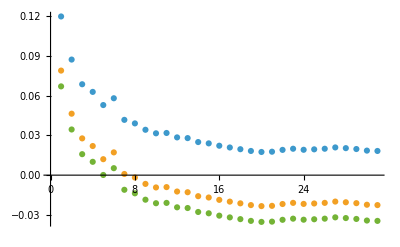

1

5

5
1 | 7
1 | 
5
1 | 11
1 | 
109
1 |  | 
5
3 |  | 
5
3 |  | 
5
1 |  | 
2
1 | 3
1 | 5
1
7
2 |  |

{0.0796046,0.0806452,0.0848075,0.0759625,0.0874089}

```mathematica
(*testo="KCCPKBGUFDPHQTYAVINRRTMVGRKDNBVFDETDGILTXRGUD
                DKOTFMBPVGEGLTGCKQRACQCWDNAWCRXIZAKFTLEWRPTYC
                QKYVXCHKFTPONCQQRHJVAJUWETMCMSPKQDYHJVDAHCTRL
                SVSKCGCZQQDZXGSFRLSWCWSJTBHAFSIASPRJAHKJRJUMV
                GKMITZHFPDISPZLVLGWTFPLKKEBDPGCEBSHCTJRWXBAFS
                PEZQNRWXCVYCGAONWDDKACKAWBBIKFTIOVKCGGHJVLNHI
                FFSQESVYCLACNVRWBBIREPBBVFEXOSCDYGZWPFDTKFQIY
                CWHJVLNHIQIBTKHJVNPIST"*)



testo="CHREEVOAHMAERATBIAXXWTNXBEEOPHBSBQMQEQERBW
RVXUOAKXAOSXXWEAHBWGJMMQMNKGRFVGXWTRZXWIAK
LXFPSKAUTEMNDCMGTSXMXBTUIADNGMGPSRELXNJELX
VRVPRTULHDNQWTWDTYGBPHXTFALJHASVBFXNGLLCHR
ZBWELEKMSJIKNBHWRJGNMGJSGLXFEYPHAGNRBIEQJT
AMRVLCRREMNDGLXRRIMGNSNRWCHRQHAEYEVTAQEBBI
PEEWEVKAKOEWADREMXMTBHHCHRTKDNVRZCHRCLQOHP
WQAIIWXNRMGWOIIFKEE"

(*
"KCCPKBGUFDPHQTYAVINRRTMVGRKDNBVFDETDGILTXRGUD
DKOTFMBPVGEGLTGCKQRACQCWDNAWCRXIZAKFTLEWRPTYC
QKYVXCHKFTPONCQQRHJVAJUWETMCMSPKQDYHJVDAHCTRL
SVSKCGCZQQDZXGSFRLSWCWSJTBHAFSIASPRJAHKJRJUMV
GKMITZHFPDISPZLVLGWTFPLKKEBDPGCEBSHCTJRWXBAFS
PEZQNRWXCVYCGAONWDDKACKAWBBIKFTIOVKCGGHJVLNHI
FFSQESVYCLACNVRWBBIREPBBVFEXOSCDYGZWPFDTKFQIY
CWHJVLNHIQIBTKHJVNPIST";*)

ciphertext=ToCode[testo];N@CoincidenceIndex[ciphertext]
ListPlot@Transpose[Table[TruncatedCoincidenceIndex[ciphertext,t,7]-{IcRND7,IcENG7,IcITA7},{t,10,Length[ciphertext],10}]]
(* ipotesi di lunghezza chiave *)
mguess=KasiskiTest[ciphertext,3]

mguess=5

(* controllo i fattori per capire se il guess è verosimile *)
Map[FactorInteger,distanze]//TableForm

(* divido il ciphertext in blocchi di testo nelle posizioni modulo mguess *)
blocks=Transpose[Partition[ciphertext,mguess]];

(* come verifica di mguess, calcolo l'índice di coincidenza per ogni blocco*)
N@Map[CoincidenceIndex,blocks]
```

```mathematica
MutualIncidence[ENG,blocks⟦3⟧]
```

0.0494833

```mathematica
"MutualIncidence = "<>ToString[MutualIncidence[ENG,Map[Dec[18,#]&,blocks⟦1⟧]]]
```

MutualIncidence = 0.0643843

```mathematica
Manipulate[
Legended[
Show[itaplot,
         PlotBlock[b][k],
LabelStyle->{GrayLevel[80]},
PlotRange->All],"MutualIncidence = "<>ToString[MutualIncidence[ENG,Map[Dec[k,#]&,blocks⟦b⟧]]]],{b,1,mguess,1},{k,0,25,1}]
```

```mathematica
mfENG=ArgMaxFreq[deng][[1,1]]
```

4

```mathematica
Map[ArgMaxFreq[Distribution[#],1]&,blocks]-mfENG
Map[ArgMaxFreq[Distribution[#],2]&,blocks]-mfENG
Map[ArgMaxFreq[Distribution[#],3]&,blocks]-mfENG
Map[ArgMaxFreq[Distribution[#],4]&,blocks]-mfENG
Map[ArgMaxFreq[Distribution[#],5]&,blocks]-mfENG
Map[ArgMaxFreq[Distribution[#],6]&,blocks]-mfENG
```

{{{18}},{{0}},{{13}},{{0}},{{19}}}

{{{-4}},{{14}},{{-4},{9}},{{8}},{{2}}}

{{{-3},{-2}},{{9},{10}},{{-4},{9}},{{4},{6},{7},{19}},{{3},{7}}}

{{{-3},{-2}},{{9},{10}},{{2},{12},{17}},{{4},{6},{7},{19}},{{3},{7}}}

{{{19}},{{3},{15}},{{2},{12},{17}},{{4},{6},{7},{19}},{{-3},{8}}}

```mathematica
{{{-1},{9},{12}},{{3},{15}},{{2},{12},{17}},{{4},{6},{7},{19}},{{-3},{8}}}
```

```mathematica
kguess={9,0,13,4,19}
FromCode[Flatten[Transpose[Mod[blocks-kguess,26]]]]
```

{9,0,13,4,19}

THEALMONDTREEWASINTENTATIVEBLOSSOMTHEDAYSWERELONGEROFTENENDINGWITHMAGNIFICENTEVENINGSOFCORRUGATEDPINKSKIESTHEHUNTINGSEASONWASOVERWITHHOUNDSANDGUNSPUTAWAYFORSIXMONTHSTHEVINEYARDSWEREBUSYAGAINASTHEWELLORGANIZEDFARMERSTREATEDTHEIRVINESANDTHEMORELACKADAISICALNEIGHBORSHURRIEDTODOTHEPRUNINGTHEYSHOULDHAVEDONEINNOVEM

```mathematica
ciphertext
```

{3,19,3,17,13,5,19,8,5,0,13,15,11,14,8,22,6,11,3,17,4,19,6,14,8,18,1,14,20,8,3,19,2,17,17,11,19,18,11,4,3,15,20,6,0,20,23,8,15,15,9,19,18,7,8,6,17,0,16,19,6,17,7,7,5,12,6,14,3,11,11,19,12,18,14,20,22,4,18,0,10,7,0,20,14,0,1,14,20,8,21,15,5,20,8,20,15,8,14,12,18,6,4,7,8,5,20,17,3,13,20,23,0,16,14,20,5,20,7,17,11,15,13,22,14,10,19,6,23,4,5,18,14,14,8,9,19,4,11,6,0,3,21,7,13,0,0,5,23,17,6,6,8,6,0,24,6,0,15,0,5,8,4,14,14,9,6,4,5,7,22,7,8,6,8,22,10,0,16,19,6,18,8,24,4,5,18,8,5,0,9,0,0,15,14,9,8,4,6,8,11,6,14,11,0,5,3,18,17,15,9,15,17,7,2,18,6,11,17,8,4,4,4,20,0,11,3,17,20,14,4,15,13,17,3,0,6,14,6,14,9,0,0,16,3,6,23,13,23,13,4,19,3,7,18,4,3,19,20,0,11,8,14,5,14,10,15,13,17,13,21,19,19,22,0,0,2,15,20,14,10,15,12,3,8,5,19,8,16,17,0,1,0,5,7,22,4,4,20,0,4,3,17,24,4,5,2,4,11,13,23,9,17,17,17,22,19,12,3,19,11,3,3,23,14,4,17,7,7,18,0,7,0,9,6,0,3,4,20,0,10,8,8,15,0,11,3,15,20,8,4,15,18,7,3,18,17,14,14,4,0,17,7,7,19,18,0,16,23,0,10,23,12,10,0,23,15,19,22,14,20,22,4,14,15,6,17,14,11,13,24,19,6,16,14,18,18,14,20,0,21,3,17,15,8,3,23,12,3,12,22,2,4,21,0,9,4,4,20,14,11,15,13,22,14,20,3,13,5,4,10,7,14,5,7,22,1,8,4,0,10,8,8,3,5,0,2,8,20,16,12,15,13,22,14,25,3,15,20,14,4,19,18,21,14,7,23,0,5,2,0,15,21,11,6,22,2,4,20,14,10,15,4,20,2,12,0,4,3,15,9,3,11,7,14,9,2,0,15,4,5,8,14,7,18,7,0,4,16,3,6,6,3,7,11,10,19,2,17,11,5,3,18,22,17,6,23,15,18,14,3,23,19,17,0,24,21,17,3,3,0,6,16,23,4,10,8,14,5,7,22,10,20,17,11,22,19,3,3,17,13,23,18,17,11,7,9,14,14,20,4,23,11,21,4,9,10,14,24,14,10,8,17,17,16,12,19,11,5,7,0,3,21,11,3,22,16,1,17,15,6,7,18,17,3,0,4,0,20,14,3,19,15,3,6,18,6,4,11,13,7,15,17,22,4,22,18,14,18,4,9,15,3,11,13,20,22,8,17,18,11,6,14,16,4,20,22,4,18,14,20,3,8,17,21,0,18,8,3,3,18,23,12,18,20,11,15,17,21,14,5,3,2,10,4,8,9,0,16,19,6,23,14,18,14,10,7,14,6,0,9,8,20,22,19,6,10,8,6,14,5,3,21,17,8,10,19,13,22,8,9,19,19,7,5,9,15,8,18,8,12,18,4,9,13,0,19,17,17,8,20,22,4,16,14,4,23,13,3,17,20,3,13,14,0,12,18,4,15,0,7,4,0,20,4,20,17,7,11,14,9,23,2,17,17,21,15,17,19,20,22,0,17,23,6,24,23,4,20,2,25,19,5,23,3,0,10,14,11,4,21,19,21,17,18,11,6,8,3,21}

```mathematica
ctx
```

{0,8,19,14,15,16,15,0,6,11,24,18,10,22,21,0,24,19,23,12,9,14,2,14,7,1,6,16,7,18,0,23,22,2,15,14,8,22,9,5,1,5,16,12,5,3,1,25,15,8,20,0,2,18,0,19,0,3,17,25,17,8,7,14,15,21,19,19,3,8,13,9,19,8,21,8,4,18,8,25,6,6,7,14,7,1,6,15,1,22,17,22,4,8,0,16,23,22,11,20,8,8,3,10,25,8,1,5,23,21,6,21,17,25,0,16,21,8,5,3,19,25,18,19,1,17,3,19,6,17,15,21,19,19,20,14,4,0,23,23,9,4,25,18,21,16,18,15,7,5,4,12,5,18,13,1,18,22,7,17,21,14,17,15,0,14,0,18,20,8,13,4,24,25,23,20,18,18,17,25,19,20,0,4,2,14,6,22,3,4,17,6,7,12,9,3,21,18,2,0,22,12,17,16,22,12,23,17,7,7,8,16,0,13,18,14,1,16,18,0,24,7,6,8,21,8,6,2,6,10,25,8,4,2,18,22,7,0,4,25,15,25,22,4,24,14,21,25,0,12,13,5,10,12,21,17,13,22,23,21,10,8,17,0,19,16,6,13,1,1,7,22,20,7,21,7,9,0,22,13,2,18,6,10,25,4,25,2,18,22,13,4,0,8,8,22,10,4,3,8,15,14,0,20,25,14,20,16,6,17,17,1,8,16,5,14,25,22,7,12,4,1,4,22,10,12,9,0,25,18,2,1,22,16,7,14,2,11,0,14,6,2,18,22,11,20,16,18,23,0,18,15,17,5,17,15,0,5,7,22,17,22,5,19,17,8,21,22,3,8,0,2,19,24,12,4,5,7,23,19,18,17,15,22,10,12,10,2,1,9,3,25,12,6,19,22,19,25,0,14,4,7,23,11,0,17,1,3,19,25,20,7,21,6,3,21,11,0,24,9,23,10,0,13,1,15,6,12,13,4,2,18,6,1,12,6,21,2,18,12,5,19,4,2,18,8,3,0,25,8,18,8,3,0,3,8,15,19,7,4,4,0,19,15,18,11,6,22,8,22,3,3,17,25,15,13,18,12,17,18,17,15,22,2,1,1,10,16,22,13,17,14,2,10,6,17,15,21,15,19,11,17,7,22,7,16,20,7,21,8,18,8,4,0,8,18,15,20,6,18,6,5,15,1,6,15,17,5,0,22,10,20,1,19,3,25,18,12,17,3,23,2,3,20,0,18,21,16,18,16,7,14,2,11,0,14,18,18,17,16,3,12,13,25,7,22,5,13,1,16,22,12,21,4,24,19,9,1,12,17,1,0,23,0,8,20,13,5,17,16,6,11,8,18,0,8,4,4,3,8,19,0,11,8,2,14,6,12,13,0,13,0,19,20,18,4,5,7,6,22,22,3,1,1,2,22,20,0,15,16,23,8,5,3,1,22,0,19,12,15,1,18,0,2,7,8,15,22,2,16,18,11,25,2,2,1,22,15,17,5,17,15,22,8,2,22,7,8,5,21,17,17,19,25,3,20,15,16,15,21,6,13,2,2,2,21,6,2,1,1,17,8,24,13,17,0,15,14,9,4,5,7,9,11,0,14,5,18,19,10,6,13,6,18,21,2,18,11,13,1,18,16,20,14,0,6,23,0,4,14,0,17,23,12,20,14,0,25,15,21,23,17,13,1,17,15,0,18,13,9,19,8,4,4,5,6,23,11,0,13,13,1,14,16,21,0,24,14,20,25,6,13,6,18,23,21,7,8,15,16,23,22,3,2,1,5,7,22,4,8,2,14,6,3,22,17,15,2,8,8,3,8,15,21,19,19,7,0,16,5,19,12,0,5,21,20,0,16,22,17,13,1,0,8,4,14,4,7,23,16,5,18,21,18,1,12,22,8,1,9,23,11,0,2,21,14,7,10,12,13,15,14,18,12,9,19,4,14}